# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll102`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"final"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
dims={412,176}
```

{412,176}

```mathematica
ims=Table[

tim=1;

nx=1+dims[[1]]*tim*i;
ny=1+dims[[2]]*tim*j;

{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{ia,ib,id,io}

,{j,Range[0,0]},{i,Range[0,0]}];

max=MinMax[Flatten[ImageData[idd]]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

max dv=38.6009

{413,177}

```mathematica
GraphicsGrid[ims[[All,All,1]],Spacings->-2]
```

-Graphics-

```mathematica
ims=Flatten[ims,1];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## More in depth

```mathematica
ImageDimensions[idd]
```

{413,177}

```mathematica
lvl=1;
```

```mathematica
k=100;
{ka,kd}=ImageData[#][[k]]&/@{iaa,idd};
pyra=pyrFuncGen[ka,lvl];

kb=Table[pyra[[1,1]][x+kd[[x]]],{x,1,1+dims[[1]]*tim}];

pyrb=pyrFuncGen[kb,lvl];


pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Test values *)
testLevels={{1,4}};
e=0.0001;
n=2;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-30];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
lt=lineTest[n,u,listv0,condition,Range[1,dims[[1]]],pyrab[[1;;1]],e,"ConstrainedCorrelation"];
```

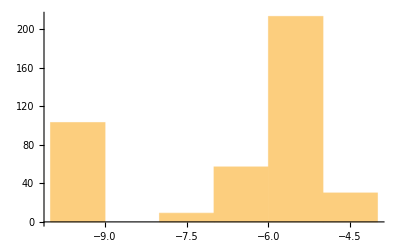

```mathematica
Histogram[Total[#]&/@lt[[All,1;;2]]]
```

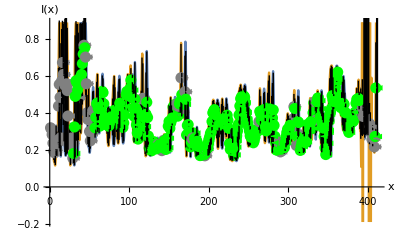

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,dims[[1]]*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

```mathematica
(*pixelIterGraphics[10,1,0,20,{{0.,0.}},condition,5, 1,pyrab[[1;;1]],e,"ConstrainedCorrelation"]*)
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],im[[3]],minmax[[2]],minmax,Range[1,1+dims[[1]]*tim,steps],Range[1,1+dims[[2]]*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g1=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g0=Rasterize[Show[im[[1]],g1,g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
levels={{1,4}};
e=0.001;
n=2;
u=0;
steps=1;
```

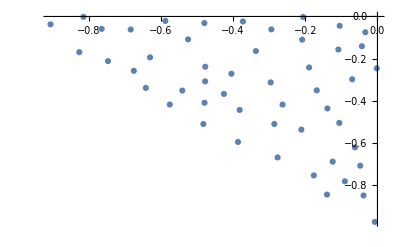

```mathematica
(* Creating list of initial Values *)
range={-10*0.1,0};
listv0=Select[RandomReal[range,{3000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0]
```

```mathematica
(* Creating condition *)
topbot={-10*0.1,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
solution = bigTest[steps,n,u,listv0,condition,e,levels,ims];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[solution]]
```

levelTable Dimensions={1,1,4}

```mathematica
solution[[1,1,1,6]];
```

### Images

```mathematica
Dimensions[ims]
```

{1,4}

```mathematica
imagesTable=Table[

groundTruth=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]]*0.1,scale,{0,1}]]}]];

ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{solution[[which,1,4]],groundTruth}],{900}]


,{which,Length[ims]}];
```

```mathematica
im1=GraphicsGrid[Partition[imagesTable[[All,1]],1],Spacings->-2];
im2=GraphicsGrid[Partition[imagesTable[[All,2]],1],Spacings->-2];
```

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
imFinal=Legended[GraphicsRow[{im1,im2},ImageSize->Large,Spacings->-25],legendBar]
```

-Graphics-

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-final-Full-lvls2-im.pdf

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

groundTruth=ImageData[-ims[[which,3]]*0.1];


density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[solution[[which,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim));

density2=(Length[Flatten[DeleteDuplicates[#]&/@Floor[solution[[which,1,2,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim));

vals=Table[
ps=Select[solution[[which,1,1,y,All,All]],1<Round[#[[1]]]<(1.+dims[[1]]*tim)&];

(ps[[All,2]]-groundTruth[[y,Round[ps[[All,1]]]]])^2

,{y,Length[solution[[which,1,1]]]}];

vals2=Table[
ps=Select[solution[[which,1,2,y,All,All]],1<Round[#[[1]]]<(1.+dims[[1]]*tim)&];

(ps[[All,2]]-groundTruth[[y,Round[ps[[All,1]]]]])^2

,{y,Length[solution[[which,1,2]]]}];

rmse=Sqrt[Mean[Join[Flatten[vals],Flatten[vals2]]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density+density2}

,{which,Length[ims]}]
```

{{RMSE= ,0.209988,Density= ,0.555328}}

### Histogram

```mathematica
fontsize=30;
imagesize=500;
maxvalue={{-1.2,0.1},{0,10000}};
```

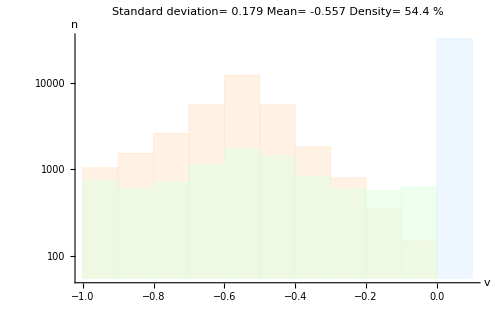

```mathematica
histogramGrid=
Table[

convergedData=Flatten[solution[[idxims,1,1,All,All,2]]];
okData=Flatten[solution[[idxims,1,2,All,All,2]]];
nonConvergedData=Flatten[solution[[idxims,1,3,All,All,2]]];

std=StandardDeviation[Join[convergedData,okData]];
mu=Mean[Join[convergedData,okData]];
density=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;
density2=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,2,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;

Histogram[{convergedData, nonConvergedData, okData},10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density+density2,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen},TicksStyle->fontsize-6]
,{idxims,Length[ims]}]
```

```mathematica
dims[[1]]*dims[[2]];
Dimensions[convergedData];
```

```mathematica
convergedData=Select[Flatten[ImageData[-ims[[1,3]]*0.1]], topbot[[1]]<#<topbot[[2]]&];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Dimensions[convergedData][[1]]/(dims[[1]]*dims[[2]]))*100.;
```

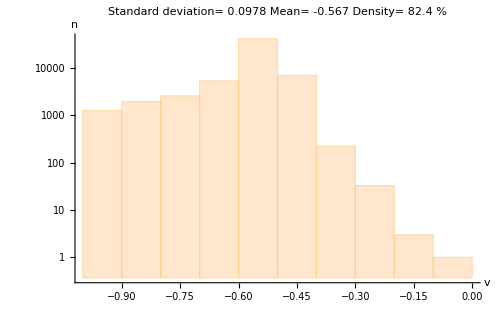

```mathematica
hGroundTruth=Histogram[convergedData,10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},
ChartStyle->{LightOrange},TicksStyle->fontsize-6]
```

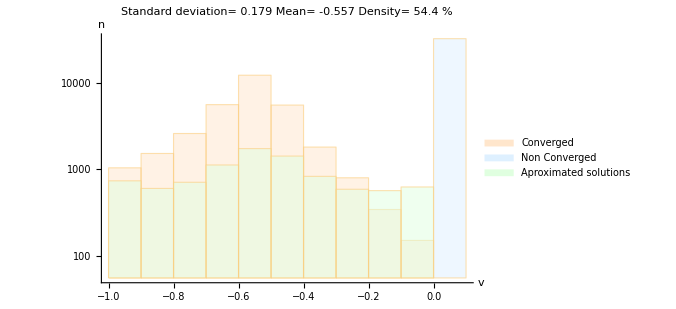
-Graphics--Graphics-

```mathematica
hFinal=Legended[
Row[{histogramGrid[[1]],hGroundTruth}],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{Style["Converged",FontSize->fontsize, FontFamily->"Times",Italic], Style["Non Converged",FontSize->fontsize, FontFamily->"Times",Italic],Style["Aproximated solutions",FontSize->fontsize, FontFamily->"Times",Italic]},LegendLayout->"Row"],Below]]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-his.pdf"}],Rasterize[hFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-final-Full-lvls2-his.pdf